Immediate and Delayed Values

There are two ways to assign a value to something in the Wolfram Language: immediate assignment (=), and delayed assignment (:=).

In immediate assignment, the value is computed immediately when the assignment is done, and is never recomputed. In delayed assignment, the computation of the value is delayed, and is done every time the value is requested.

As a simple example, consider the difference between value=RandomColor[ ] and value:=RandomColor[ ].

In immediate assignment (=), a random color is immediately generated:

```mathematica
value=RandomColor[ ]
```

RGBColor[0.5776360098335713, 0.16742506587239303, 0.23693496006313164]

Every time you ask for value, you get the same random color:

```mathematica
value
```

RGBColor[0.5776360098335713, 0.16742506587239303, 0.23693496006313164]

In delayed assignment (:=), no random color is immediately generated:

```mathematica
value:=RandomColor[ ]
```

Each time you ask for value, RandomColor[ ] is computed, and a new color is generated:

```mathematica
value
```

RGBColor[0.8431574152311205, 0.8848301850335125, 0.4749471491092443]

The color will typically be different every time:

```mathematica
value
```

RGBColor[0.7127712074377826, 0.37013138983058824, 0.9880717025911983]

It’s very common to use := if something isn’t ready yet when you’re defining a value.

You can make a delayed assignment for circles even though n doesn’t yet have a value:

```mathematica
circles:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
```

Give n a value:

```mathematica
n=6
```

6

Now you can ask for circles and the value you’ve given for n will be used:

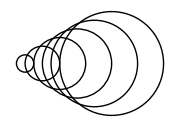

```mathematica
circles
```

The idea of delayed assignment is directly analogous to the Delayed construct we discussed for deploying webpages. In delayed assignment we don’t compute a value until we need it. Similarly, when we use CloudPublish with Delayed we don’t compute the content of a webpage until someone asks for it.

There’s a notion of delayed rules too. x→rhs computes rhs immediately. But in a delayed rule x:>rhs (typed :>), rhs is instead recomputed every time it’s requested.

This is an immediate rule, where a specific value for RandomReal[ ] is immediately computed:

```mathematica
x->RandomReal[ ]
```

x→0.522293

You can replace four x’s, but they’ll all be the same:

```mathematica
{x,x,x,x}/.x->RandomReal[ ]
```

{0.821639,0.821639,0.821639,0.821639}

This is a delayed rule, where the computation of RandomReal[ ] is delayed:

```mathematica
x:>RandomReal[ ]
```

x:>RandomReal[ ]

RandomReal[ ] is computed separately when each x is replaced, giving four different values:

```mathematica
{x,x,x,x}/.x:>RandomReal[ ]
```

{0.536115,0.84214,0.242933,0.514131}

Vocabulary

x:=value |   | delayed assignment, evaluated every time x is requested
x:>value |   | delayed rule, evaluated every time x is encountered (typed :>)

"2 Exercises Available" | "Get Started »"

Replace x in {x,x+1,x+2,x^2} by the same random integer up to 100. »

| Sample expected output: |  
  | {97,98,99,9409} |

Replace each x in {x,x+1,x+2,x^2} by a separately chosen random integer up to 100. »

| Sample expected output: |  
  | {100,3,38,7225} |

Q&A

Why not always use :=?

Because you don’t want to have to recompute things unless it’s necessary. It’s more efficient to just compute something once, then use the result over and over again.

How does one read := and :> out loud?

:= is usually just “colon equals”, though sometimes “delayed assignment”. :> is usually “colon greater”, though sometimes “delayed rule”.

What happens if I do x=x+1, with x not having a value?

You’ll start an infinite loop that’ll eventually get cut off by the system. x={x} is the same story.

What’s the significance of inputs being labeled In[n]:=, and outputs Out[n]= ?

It indicates that inputs are assigned to In[n] and outputs to Out[n]. The := for input means the assignment is delayed, so that if you ask for In[n] the result will be recomputed.

Tech Notes

In the Wolfram Language, the process of computing results is often called evaluation, because it involves finding values of things.

The Wolfram Language has many ways of controlling evaluation. An example is the function Hold, which maintains an expression in “held” form until it is “released”.

The internal form of x=y is Set[x,y]. x:=y is SetDelayed[x,y]. x:>y is RuleDelayed[x,y].